### Inicialización

#### Para escribir la hora y los tiempos

```mathematica
paded[j_]:=StringJoin[Take[Characters[" "<>ToString[j]],-2] ]
zeropaded[j_]:=StringJoin[Take[Characters["0"<>ToString[j]],-2] ]
padedsec[j_]:=StringJoin[Take[Characters[" "<>ToString[j]],-5] ]
```

```mathematica
currenttime:=StringTake[DateString[],-8];
currentday:=StringTake[StringTake[DateString[],15],-11]
hms[s_]:={Floor[s/3600],Floor[(s-3600Floor[s/3600])/60],s-3600Floor[s/3600]-60.Floor[(s-3600Floor[s/3600])/60]};
strhm[s_]:=If[s<60,"<1m",If[hms[s]⟦1⟧==0,ToString[hms[s]⟦2⟧]<>"m",
ToString[hms[s]⟦1⟧]<>"h "<>paded[hms[s]⟦2⟧]<>"m"]];
strhms[ss_]:=Block[{s=Round[ss]},If[ss<0.01,"<"<>ToString[0.01]<>"s",If[ss<60,ToString[NumberForm[hms[ss]⟦3⟧,{4,2}]]<>"s",If[hms[s]⟦1⟧==0,ToString[hms[s]⟦2⟧]<>"m "<>ToString[Round[hms[s]⟦3⟧,1]]<>"s",ToString[hms[s]⟦1⟧]<>"h "<>paded[hms[s]⟦2⟧]<>"m "<>ToString[Round[hms[s]⟦3⟧,1]]<>"s"]]]];
strhmscolon[s_]:=If[s>100000,"?...",If[s<0.01,"0",zeropaded[hms[s]⟦1⟧]<>":"<>zeropaded[hms[s]⟦2⟧]<>":"<>zeropaded[Round[hms[s]⟦3⟧,1]]],"?..."];
```

#### Set current directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Notebook final de Jose retocado

• Se expresan los valores de parámetros en forma exacta (5/10 en vez de 0.5 etc.), 
• Se calcula el tiempo que tardan los cálculos más largos, 
• Se “calcula” el índice de la solución real positiva (lo que puede ahorrar problemas cuando cambien las soluciones y la real positiva no sea la segunda), 
• Se simplifican las soluciones y se guardan en ficheros.

```mathematica
(*Ecuaciones en el equilibrio de C0 a C5 y S (llamada aquí C6)*)
ecuac={
0==kon Peq*Teq-(koff+kp) C0+(b+γ (a*C1*ST)/(a*C1+1)) C1,
0==kp C0-(koff+kp+b+γ (a*C1*ST)/(a*C1+1)) C1+(b+γ (a*C1*ST)/(a*C1+1)) C2,
0==kp C1-(koff+kp+b+γ (a*C1*ST)/(a*C1+1)) C2+(b+γ (a*C1*ST)/(a*C1+1)) C3,
0==kp C2-(koff+kp+b+γ (a*C1*ST)/(a*C1+1)) C3+(b+γ (a*C1*ST)/(a*C1+1)) C4,
0==kp C3-(koff+kp+b+γ (a*C1*ST)/(a*C1+1)) C4+(b+γ (a*C1*ST)/(a*C1+1)) C5,
0==kp C4-(koff+b+γ (a*C1*ST)/(a*C1+1)) C5
}//.γ (a*C1*ST)/(a*C1+1)->C6;
sept={0==C6(a*C1+1)-γ a*C1*ST};
ecuaciones=Join[ecuac,sept];
TableForm[ecuaciones]
```

0==C1 (b+C6)-C0 (koff+kp)+kon Peq Teq
0==C2 (b+C6)+C0 kp-C1 (b+C6+koff+kp)
0==C3 (b+C6)+C1 kp-C2 (b+C6+koff+kp)
0==C4 (b+C6)+C2 kp-C3 (b+C6+koff+kp)
0==C5 (b+C6)+C3 kp-C4 (b+C6+koff+kp)
0==-C5 (b+C6+koff)+C4 kp
0==(1+a C1) C6-a C1 ST γ

```mathematica
(*Solución simbólica de C0 a C6 en el equilibrio (tarda unos 20s).*)
Timing[soluc=Solve[ecuaciones,{C0,C1,C2,C3,C4,C5,C6}]][[1]]//strhms
```

strhms[30.625]

```mathematica
Clear[PT,TT,Peq,Teq,kon,koff,kp,b,γ,TT,ST,a]
parametersFull={kon->10^-5,koff->5 10^-2,kp->9 10^-2,b->4 10^-2,γ->10^-6,TT-> 3 10^4,ST->6 10^5,a->2 10^-3};
(*Solución de P y T en el equilibrio*)
solPyT=Solve[{0==-kon Peq Teq+koff (PT-Peq),0==-kon Peq Teq+koff (TT-Teq)},{Peq,Teq}][[2]]//FullSimplify;
(*parámetros con Peq y Teq*)
parametrosconPeqyTeq=Join[parametersFull,solPyT//.parametersFull]//FullSimplify
```

{kon→1/100000,koff→1/20,kp→9/100,b→1/25,γ→1/1000000,TT→30000,ST→600000,a→1/500,Peq→1/2 (-35000+PT+√(1225000000+(-50000+PT) PT)),Teq→1/2 (25000-PT+√(1225000000+(-50000+PT) PT))}

```mathematica
{kon->1/100000,koff->1/20,kp->9/100,b->1/25,γ->1/1000000,TT->30000,ST->600000,a->1/500,Peq->1/2 (-35000+PT+√(1225000000+(-50000+PT) PT)),Teq->1/2 (25000-PT+√(1225000000+(-50000+PT) PT))}
```

{kon→1/100000,koff→1/20,kp→9/100,b→1/25,γ→1/1000000,TT→30000,ST→600000,a→1/500,Peq→1/2 (-35000+PT+√(1225000000+(-50000+PT) PT)),Teq→1/2 (25000-PT+√(1225000000+(-50000+PT) PT))}

(*comprobación de que la solución 2 es la única Real y positiva*)
i=3;PT=10^3;
Timing[solsC5=soluc[[i,6,2]]//.parametrosconPeqyTeq][[1]]//strhms
If[solsC5∈Reals,TrueQ[solsC5>0],False]
i=.

```mathematica
(* buscamos la solución en que C5 es Real y positivo (tarda unos 20s) *)
valPT=PT->10^3;
{Timing[sols=soluc[[All,6,2]]//.parametrosconPeqyTeq//.valPT][[1]]//strhms,
t=Table[If[sols[[i]]∈Reals,TrueQ[sols[[i]]>0],False],{i,Length[soluc]}]}
```

{strhms[34.2969],{False,True,False,False,False,False}}

```mathematica
{Timing[solsC4=soluc[[All,5,2]]//.parametrosconPeqyTeq//.valPT][[1]]//strhms,tC4=Table[If[solsC4[[i]]∈Reals,TrueQ[solsC4[[i]]>0],False],{i,Length[soluc]}]}
```

{strhms[35.6719],{True,True,False,False,False,False}}

```mathematica
{Timing[solsC3=soluc[[All,4,2]]//.parametrosconPeqyTeq//.valPT][[1]]//strhms,tC3=Table[If[solsC3[[i]]∈Reals,TrueQ[solsC3[[i]]>0],False],{i,Length[soluc]}]}
```

{strhms[29.8281],{False,True,False,False,False,False}}

```mathematica
solsC5=soluc[[Flatten[Position[t,True]][[1]],6,2]]//.parametrosconPeqyTeq//Simplify;
```

```mathematica
solsC4=soluc[[Flatten[Position[tC4,True]][[1]],5,2]]//.parametrosconPeqyTeq//Simplify;
```

```mathematica
solsC3=soluc[[Flatten[Position[tC3,True]][[1]],4,2]]//.parametrosconPeqyTeq//Simplify;
```

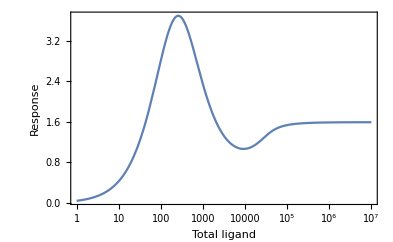

```mathematica
(*definición de C5 en el equilibrio en función de PT*)
C5eqLTT[x_]:=solsC5/.PT->x
(*gráfica de C5 en el equilibrio en función de PT*)
LogLinearPlot[C5eqLTT[LT],{LT,1,10^7},PlotRange->All,Frame->True,FrameLabel->{"Total ligand","Response"},LabelStyle->{Bold,14}]
```

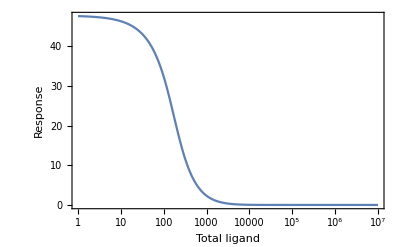

```mathematica
(*Definición de C4 en el equilibrio en función de PT*)
C4eqLTT[x_]:=solsC4/. PT->x
(*Gráfica de C4 en el equilibrio en función de PT*)
LogLinearPlot[C4eqLTT[LT],{LT,1,10^7},PlotRange->All,Frame->True,FrameLabel->{"Total ligand","Response"},LabelStyle->{Bold,14}]
```

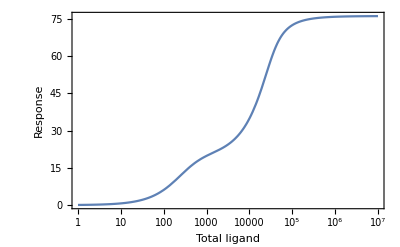

```mathematica
(*Definición de C3 en el equilibrio en función de PT*)
C3eqLTT[x_]:=solsC3/. PT->x

(*Gráfica de C3 en el equilibrio en función de PT*)
LogLinearPlot[C3eqLTT[LT],{LT,1,10^7},PlotRange->All,Frame->True,FrameLabel->{"Total ligand","Response"},LabelStyle->{Bold,14}]
```

```mathematica
nn=5;
rr=3;
kk=2;
```

```mathematica
(Rsol={solsC3,solsC4,solsC5}*Table[Exp[-kk*(nn-i)],{i,nn-rr+1,nn}]/. List->Plus;)
```

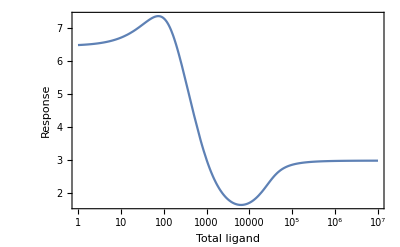

```mathematica
ReqLTT[x_]:=Rsol/. PT->x
LogLinearPlot[ReqLTT[LT],{LT,1,10^7},PlotRange->All,Frame->True,FrameLabel->{"Total ligand","Response"},LabelStyle->{Bold,14}]
```

```mathematica
DERNUMERICA = D[Rsol,PT];
soluciones=NSolve[DERNUMERICA==0,PT]
```

$Aborted

```mathematica
(*Sólo las soluciones reales*)
realSolutions=Select[soluciones,FreeQ[#,Complex]&]
```

{{PT→9208.},{PT→-366.769},{PT→259.087}}

```mathematica
(*Valor de la respuesta para el valor de ligando que da el Emax*)
Emax=N[solsC5/. PT->259.0869996159376]
```

3.68855

```mathematica
EmaxHalf = Emax/2
```

1.84428

```mathematica
EC50 = NSolve[solsC5 == EmaxHalf, PT]
```

{{PT→1551.14},{PT→52.4939}}

```mathematica
(*DE MANERA SIMBÓLICA*)
C5expr=C5/. soluc;
```

```mathematica
C5exprT=C5expr/. solPyT//Simplify;
```

```mathematica
dC5dPT=D[C5exprT,PT];
```

```mathematica
soluciones=NSolve[dC5dPT==0,PT];
```

$Aborted